```mathematica
$Path=Prepend[$Path,"E:\\HOME\\anton\\roundabout"];
```

```mathematica
<<"ACPackages`"
<<"ErrorBarPlots`"
```

```mathematica
$WD=SetWorkDir[];
```

```mathematica
$WD=NotebookDirectory[];
```

```mathematica
SetWorkDir["/2006.07.20/Re=10"];
```

```mathematica
(*Table of results: list of {date(year,month,day),mesh(Nx=Nz),Re,r/R,gamma,F(r),Coriolis;shift,mvx,δmvx,mvy,δmvy,mvz,δmvz,Evx,δEvx,Evy,δEvy,Evz,δEvz,mψ,δmψ,comment}*)
indepkol=9;
depkol=15;
```

## Добавление записей

```mathematica
dvx=dvy=dvz=0;
dqvx=dqvy=dqvz=0;
```

```mathematica
{dvx,dvy,dvz,dqvx,dqvy,dqvz}={2 10^-5,1 10^-4,2 10^-5,5 10^-6,2 10^-5,2 10^-6};
```

```mathematica
{dvx,dvy,dvz,dqvx,dqvy,dqvz}={0,6 10^-5,0,0,2 10^-5,0};
```

```mathematica
putlist=Join[{2010,12,16},{256},{Rm=115,kappa=0.5,gamma=10^-4,Fr="dp1",Coriolis=0,shift,maxvx,dvx,maxvy,dvy,maxvz,dvz,mqvx,dqvx,mqvy,dqvy,mqvz,dqvz,Max[Abs[ψ]],Max[Abs[ψ2-ψ1]],"ErrScale 1e-4"}]/.b_:>CForm[b]/;NumericQ[b]
```

{2010,12,16,256,115,0.5,0.0001,dp1,0,0.4111946309734112,0.13345372743418532,0.00002,0.5394917991670589,0.0001,0.0939417424156275,0.00002,0.0031174654488904095,5.e-6,0.11665792960566573,0.00002,0.001136343580263234,2.e-6,0.04115338165082248,0.0013980584104512864,ErrScale 1e-4}

```mathematica
putlist>>>($WD<>"\\result.dat")
{Rm,kappa,gamma,Fr,Coriolis,shift,maxvx,dvx,maxvy,dvy,maxvz,dvz,mqvx,dqvx,mqvy,dqvy,mqvz,dqvz,ψ,ψ2,ψ1}=.;
```

## Анализ записей

### Функции

```mathematica
UpdateData:=Block[{},Print[fields=Module[{res,stm},res=ReadList[stm=StringToStream[First[ReadList[$WD<>"\\result.dat"]]],Word,WordSeparators->{" ",",","{","}"}];Close[stm];res]];
all=Select[Rest[ReadList[$WD<>"\\result.dat"]]/.{a_+b_ E->b*10^a}/.{a_+b_ e->b*10^a},StringFreeQ[Last[#],"wrong"]&];
Print["Total:",Length[all]," records"];]
```

```mathematica
MakeRule[el_]:=MapThread[Rule,{fields,el}];
```

```mathematica
ShowDependance[param_,funcs_,conditions_List:{},viv_:True]:=Block[{allbut=GetResults[conditions,viv],dep,deplist,numpar,othern,otherv},If[FreeQ[Drop[fields,{indepkol+1,-2}],param],Print["Wrong parameter"];Return[]];numpar=First[Flatten[Position[fields,param]]];othern=Complement[Join[Range[4,Length[fields]-depkol-1],{Length[fields]}],{numpar}];If[viv,Print["All such parameters=",Union[(#1⟦numpar⟧&)/@allbut]]];dep=First[Rest[Reap[(Sow[#1,NotList@@#1⟦othern⟧]&)/@Sort[allbut,N[#1⟦numpar⟧]<N[#2⟦numpar⟧]&],_,f]]];dep=Select[dep,Length[Last[#1]]>1&];
(*Print["dep=",dep];*)
otherv=Drop[Drop[Drop[fields,{indepkol+1,-2}],{numpar}],3];If[viv,Print[otherv]];nom=0;If[Length[dep]==0,Print["Data was not found"];Return[]];If[viv,Print["Plots can be shown for parameters:"]];(Print["№",++nom,":",MapThread[Rule,{otherv,List@@First[#1]}],", number of points=",Length[Last[#1]]]&)/@dep;If[Length[dep]>1,nom=Input["Введите номер желаемой зависимости"],nom=1];
If[viv,Print["So constant parameters are:\t",Thread[otherv->List@@First[dep⟦nom⟧]]]];deplist=({#1,"δ"<>#1," "<>#1}&)/@Flatten[{funcs}];pts=Join[{param},RotateRight/@deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];pts=Function[l,{({{#1⟦1⟧,#1⟦2⟧},ErrorBar[#1⟦3⟧]}&)/@Flatten/@Transpose[Join[{First/@pts},{l}]],l⟦1,-1⟧}]/@Transpose[deplist/.MakeRule/@Last[dep⟦nom⟧]];
pts=Join[{param},deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];(*If[param≠Last[fields],(ListPlot[{First[#1]},AxesLabel->{param,Last[#1]},Axes->True,Frame->False,PlotLabel->Last[#1],PlotMarkers->{■}]&)/@pts];*)
If[param≠Last[fields],ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All]&/@Transpose[pts[[All,2;;-2]]]
]
];
```

```mathematica
ShowDependanceMod[param_,funcs_,conditions_List:{}]:=Block[{allbut=GetResults[conditions],dep,deplist,numpar,othern,otherv},
numpar=First[Flatten[Position[fields,param]]];othern=Complement[Join[Range[4,Length[fields]-depkol-1],{Length[fields]}],{numpar}];dep=First[Rest[Reap[(Sow[#1,NotList@@#1⟦othern⟧]&)/@Sort[allbut,N[#1⟦numpar⟧]<N[#2⟦numpar⟧]&],_,f]]];dep=Select[dep,Length[Last[#1]]>1&];
otherv=Drop[Drop[Drop[fields,{indepkol+1,-2}],{numpar}],3];nom=0;If[Length[dep]==0,Print["Data was not found"];Return[]];(*(Print["№",++nom,":",MapThread[Rule,{otherv,List@@First[#1]}],", number of points=",Length[Last[#1]]]&)/@dep;*)
nom=1;
deplist=({#1,"δ"<>#1," "<>#1}&)/@Flatten[{funcs}];pts=Join[{param},RotateRight/@deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];pts=Function[l,{({{#1⟦1⟧,#1⟦2⟧},ErrorBar[#1⟦3⟧]}&)/@Flatten/@Transpose[Join[{First/@pts},{l}]],l⟦1,-1⟧}]/@Transpose[deplist/.MakeRule/@Last[dep⟦nom⟧]];
pts=Join[{param},deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];(*If[param≠Last[fields],(ListPlot[{First[#1]},AxesLabel->{param,Last[#1]},Axes->True,Frame->False,PlotLabel->Last[#1],PlotMarkers->{■}]&)/@pts];*)
If[param≠Last[fields],Sow[ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All],StringDrop[#⟦-1,-1⟧,1]]&/@Transpose[pts[[All,2;;-2]]]
]
];
```

```mathematica
GetResults[conditions_List:{},viv_:False]:=Block[{pattern,rules=Union[Select[conditions,Head[#]==Rule&]],
(*Unequal doesn't work always*)
ineqs=And@@Flatten[Select[conditions,MemberQ[{Less,LessEqual,Greater,GreaterEqual,Unequal},Head[#]]∨#==False&]]},
MatchesQ[el_]:=Module[{mr=MakeRule[el]},Simplify[ineqs/.mr]∧Complement[rules,mr]=={}];
If[viv,Print["All data matches (",Simplify[ineqs],")",Sequence@@("&&("<>First[#]<>"="<>ToString[InputForm[Last[#]]]<>")"&/@rules),":"]];
Return[Select[all,MatchesQ]];
];
```

### Действия

```mathematica
UpdateData
```

{year,month,day,Nxz,Re,r/R,gamma,F(r),Coriolis,shift,mvx,δmvx,mvy,δmvy,mvz,δmvz,Evx,δEvx,Evy,δEvy,Evz,δEvz,mψ,δmψ,comment}

Total:403 records

```mathematica
$res=GetResults[{"r/R"->0.25,"Re"<=100}]
```

All data matches (Re≤100)&&(r/R=0.25):

```mathematica
$res=GetResults[{"F(r)"->"r"}];Length[$res]
```

150

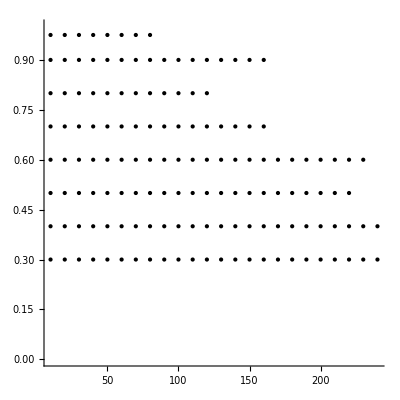

```mathematica
Graphics[Point/@Union[GetFields[#,{"Re","r/R"}]&/@$res],AspectRatio->1,Axes->True,AxesOrigin->{0,0},PlotRange->{0,1}]
```

```mathematica
Union[4First[#] √(2Last[#])&/@Union[GetFields[#,{"Re","r/R"}]&/@$res]]
```

{30.9839,35.7771,40.,43.8178,47.3286,50.5964,53.6656,55.857,61.9677,71.5542,80.,87.6356,92.9516,94.6573,101.193,107.331,107.331,111.714,120.,123.935,131.453,141.986,143.108,151.789,154.919,160.,160.997,167.571,175.271,178.885,185.903,189.315,200.,202.386,214.663,214.663,216.887,219.089,223.428,236.643,240.,247.871,250.44,252.982,262.907,268.328,278.855,279.285,280.,283.972,286.217,303.579,306.725,309.839,320.,321.994,331.3,335.142,340.823,350.542,354.175,357.771,360.,371.806,375.659,378.629,390.999,393.548,394.36,400.,402.79,404.772,425.958,429.325,429.325,433.774,438.178,440.,446.856,455.368,464.758,465.102,473.286,480.,481.996,482.991,495.742,500.879,505.964,520.,520.615,525.814,526.726,536.656,556.561,557.71,560.,567.944,569.631,572.433,588.693,590.322,600.,607.157,608.21,613.449,615.272,619.677,640.,643.988,650.661,657.267,662.601,679.765,680.,681.645,697.653,701.085,709.93,712.629,715.542,720.,743.613,744.903,751.319,757.258,760.,787.096,800.,804.984,822.873,840.,858.65,858.65,880.}

```mathematica
GetResults[{"Nxz"->128,"Ny"->5,"r/R"->1/4,"lfi"->1.,"F(r)"->1,"Coriolis"->0,"comment"->"ErrScale 1e-4"}]
```

```mathematica
ShowTable[$res,{"Nxz","Re","r/R","F(r)","shift","mvx","mvy","mvz","Evx","Evy","Evz","mψ"}]
```

Nxz | Re | r/R | F(r) | shift | mvx | mvy | mvz | Evx | Evy | Evz | mψ | F(r)
10 | 1 | 0.25 | dp | -0.094552 | 0.00350882 | 1.01033 | 0.00210355 | 2.09116×10^-6 | 0.272792 | 7.02428×10^-7 | 0.00120475 | dp
20 | 1 | 0.25 | dp | -0.0945432 | 0.00351808 | 1.00443 | 0.00195735 | 1.8201×10^-6 | 0.264418 | 6.02702×10^-7 | 0.00110386 | dp
30 | 1 | 0.25 | dp | -0.0946276 | 0.00351412 | 1.00484 | 0.00193835 | 1.74952×10^-6 | 0.262043 | 5.87322×10^-7 | 0.00108016 | dp
40 | 1 | 0.25 | dp | -0.0941067 | 0.00351162 | 1.0034 | 0.00192664 | 1.71451×10^-6 | 0.260802 | 5.75338×10^-7 | 0.00104135 | dp
50 | 1 | 0.25 | dp | -0.0943027 | 0.00350824 | 1.00345 | 0.00192126 | 1.70257×10^-6 | 0.260389 | 5.72839×10^-7 | 0.00103956 | dp
60 | 1 | 0.25 | dp | -0.0939171 | 0.00350948 | 1.00312 | 0.00191966 | 1.69475×10^-6 | 0.260114 | 5.70822×10^-7 | 0.00103207 | dp
70 | 1 | 0.25 | dp | -0.0941415 | 0.00350822 | 1.00309 | 0.00191712 | 1.69018×10^-6 | 0.259961 | 5.69165×10^-7 | 0.00102745 | dp
80 | 1 | 0.25 | dp | -0.0942282 | 0.00350792 | 1.00302 | 0.00191892 | 1.68782×10^-6 | 0.259878 | 5.6892×10^-7 | 0.00101974 | dp
90 | 1 | 0.25 | dp | -0.0950098 | 0.00350851 | 1.00298 | 0.00191738 | 1.68586×10^-6 | 0.259811 | 5.6856×10^-7 | 0.00102088 | dp
100 | 1 | 0.25 | dp | -0.0942004 | 0.00350774 | 1.00294 | 0.00191796 | 1.68428×10^-6 | 0.259753 | 5.67998×10^-7 | 0.00101706 | dp
110 | 1 | 0.25 | dp | -0.0939752 | 0.00350851 | 1.00298 | 0.00191737 | 1.68586×10^-6 | 0.259811 | 5.6856×10^-7 | 0.00101915 | dp

#### Все поля определённого типа

```mathematica
GetField[res_,field_String]:=Block[{num=Position[fields,field]},
If[Length[num]<1,Print["Field not found"];Return[$Failed]];
Extract[res,First[num]]
]
GetFields[res_,fs_List]:=GetField[res,#]&/@fs
ShowTable[fromres_,fs_List]:=Prepend[GetFields[#,fs]&/@fromres,fs]//TableForm
```

```mathematica
GetField[Union/@Transpose[$res],"F(r)"]
```

{1,dp,dp1,epsr}

```mathematica
MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res]}]//TableForm
```

```mathematica
Select[MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res]}],Length[#]>3&]//TableForm
```

### Зависимости

```mathematica
allfuncs=Select[Take[fields,{indepkol+1,-2}],Length[StringPosition[#,"δ"]]==0&]
```

{shift,mvx,mvy,mvz,Evx,Evy,Evz,mψ}

```mathematica
ShowDependance["r/R",allfuncs,{"F(r)"->"1","Re"->50}]
```

All data matches (True)&&(F(r)="1")&&(Re=50):

All such parameters={0.5,0.6,0.7,0.8,0.9,0.975}

{Nxz,Re,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→256,Re→50,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=6

So constant parameters are:	{Nxz→256,Re→50,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

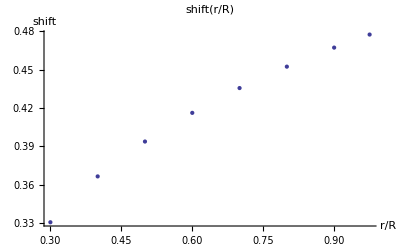
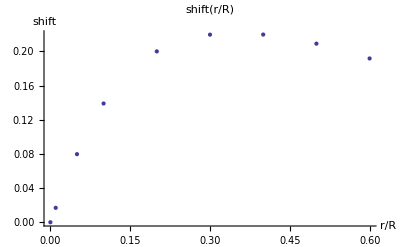
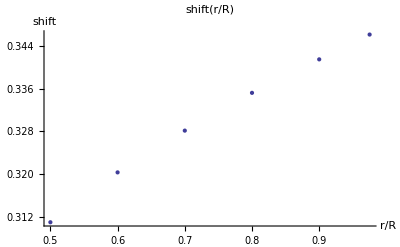
```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

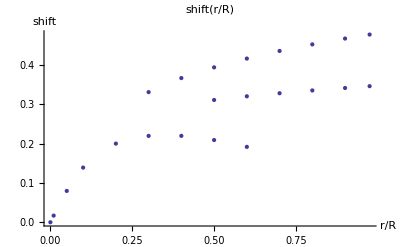

All data matches (True)&&(F(r)="dp")&&(r/R=0.3):

All such parameters={1,10,20,30,40,50,60,70,80,90,100}

{Nxz,r/R,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→128,r/R→0.3,gamma→0.0001,F(r)→dp,Coriolis→0,comment→ErrScale 1e-4}, number of points=12

So constant parameters are:	{Nxz→128,r/R→0.3,gamma→0.0001,F(r)→dp,Coriolis→0,comment→ErrScale 1e-4}

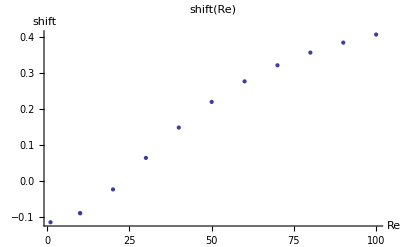
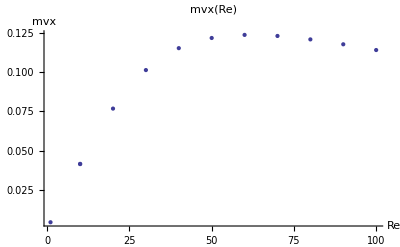
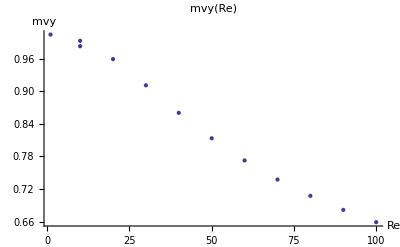
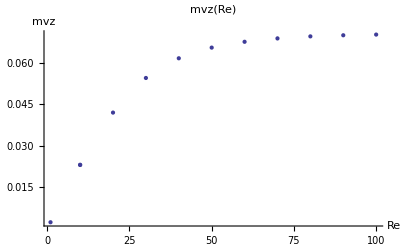
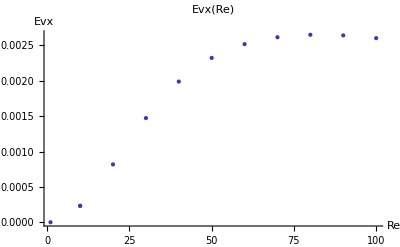
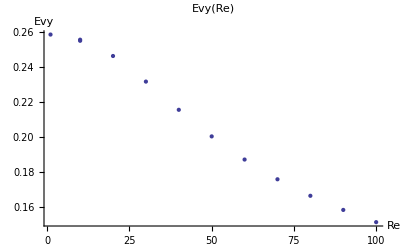
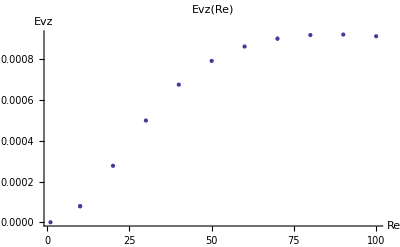
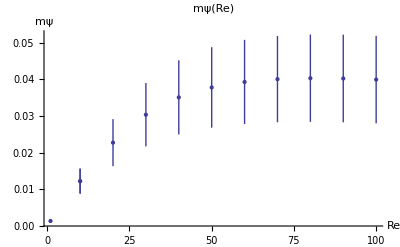

```mathematica
ShowDependance["Re",allfuncs,{"F(r)"->"dp","r/R"->0.3}]
```

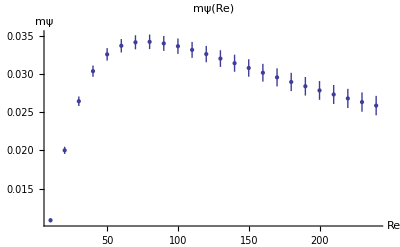
```mathematica
Show[-Graphics-,-Graphics-]
```

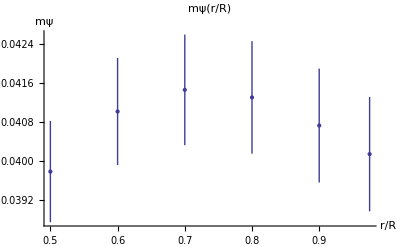
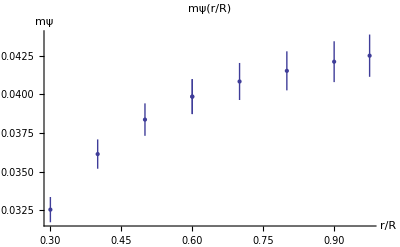
```mathematica
Show[-Graphics-,-Graphics-]
```

#### Результаты

"F(r)=1; Re=50"

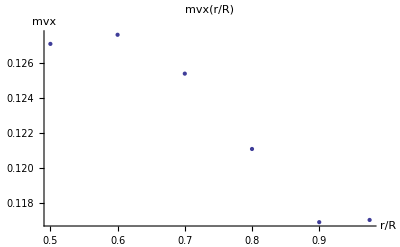
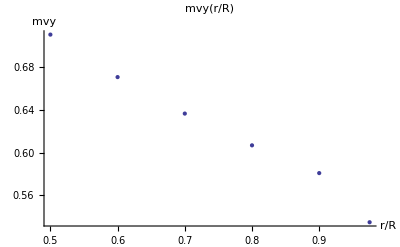
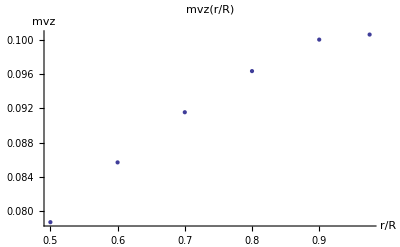
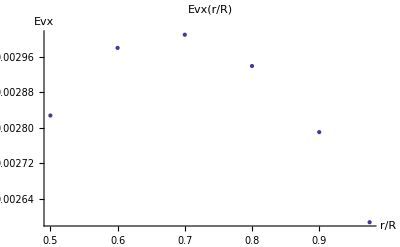
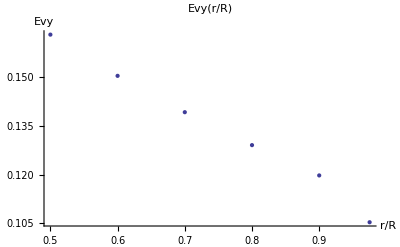
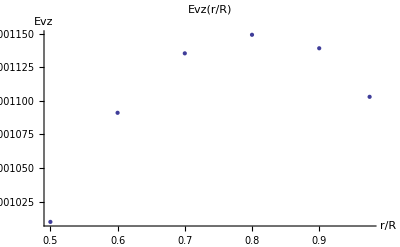
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

"F(r)=r; Re=50"

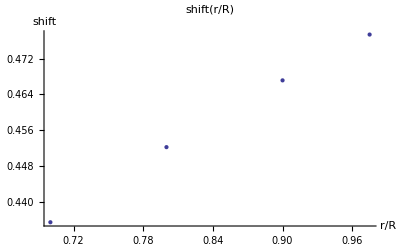
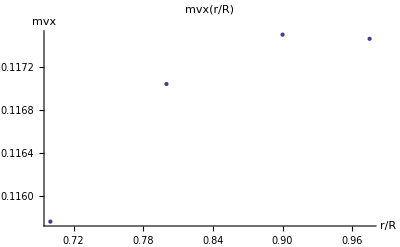
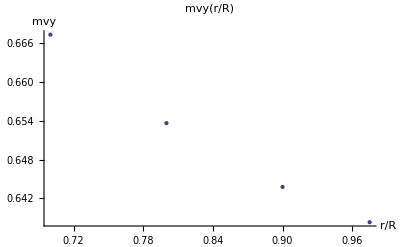
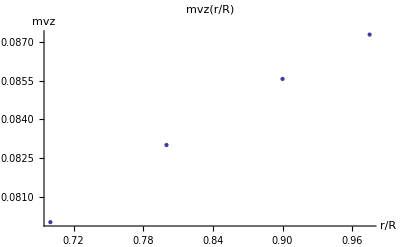
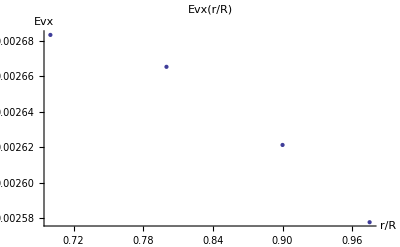
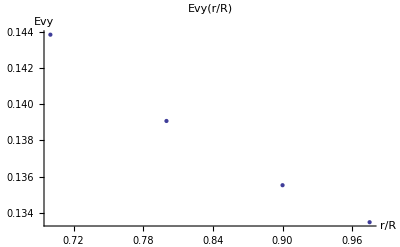
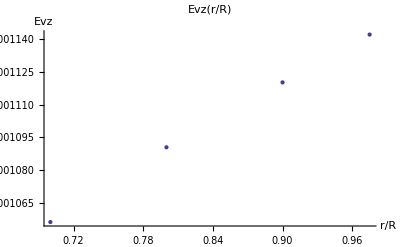
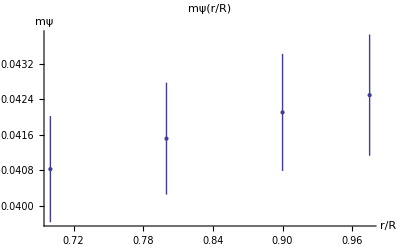

"F(r)=dp; Re=50"

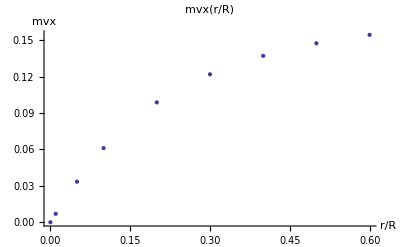
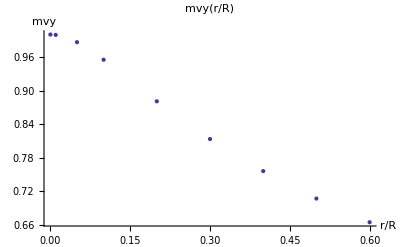
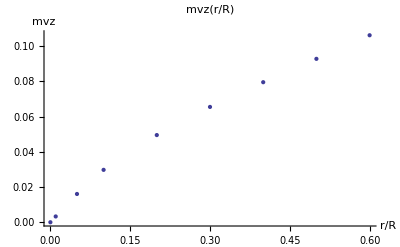
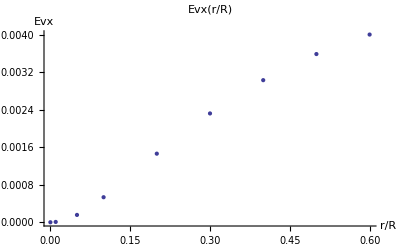
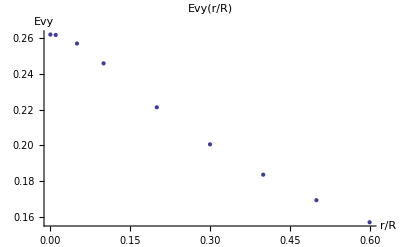
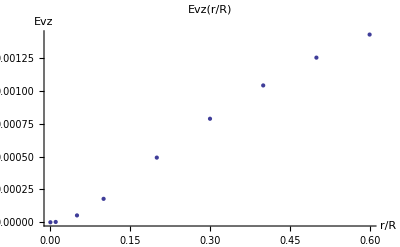
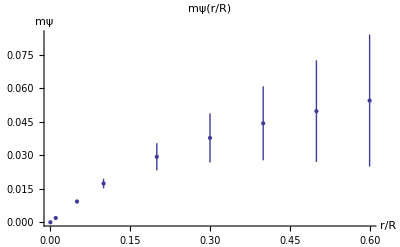
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

"F(r)=1"; Re=80

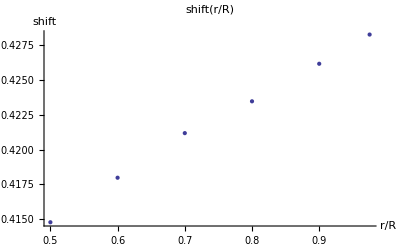
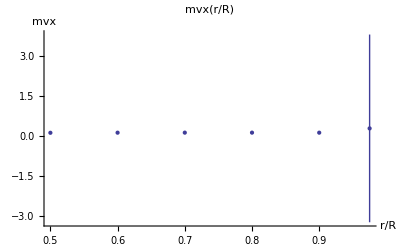
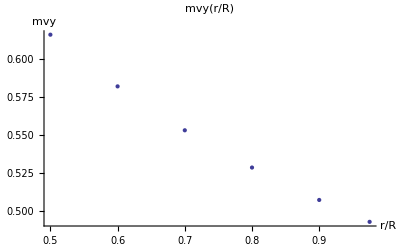
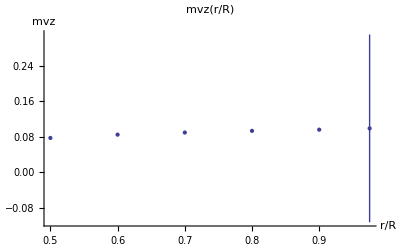
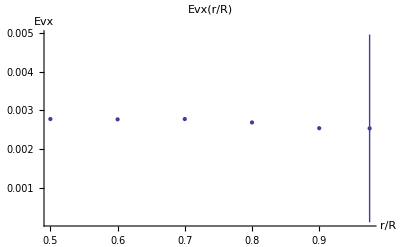
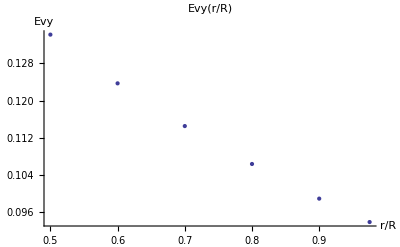
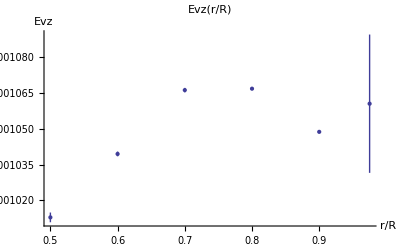
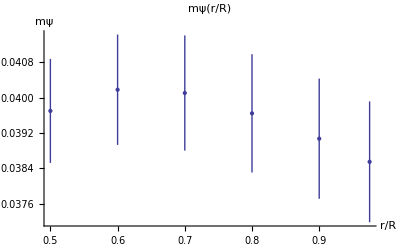

"F(r)=dp"; Re=80

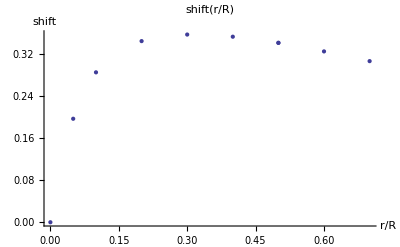
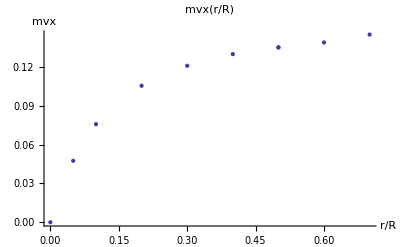
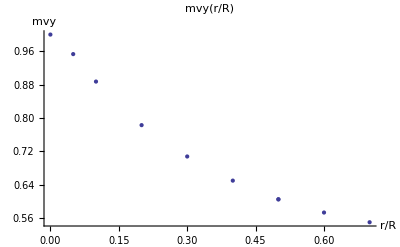
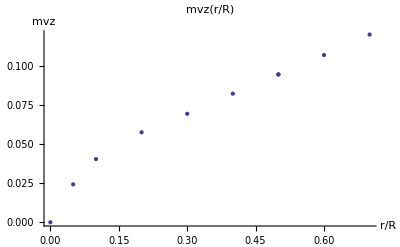
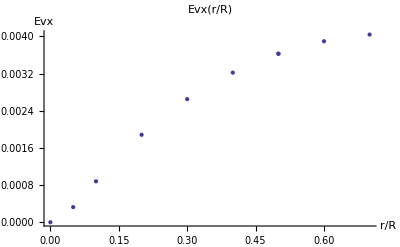
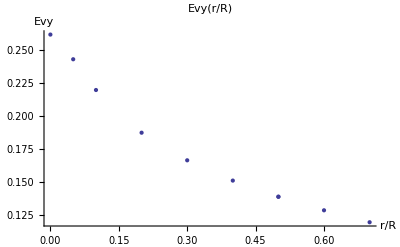
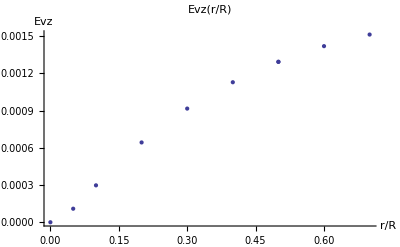
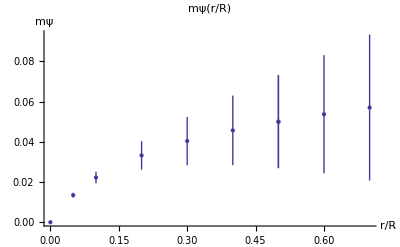

#### Подбор результатов

```mathematica
funcs={};
Block[{allbut=GetResults[{},False]},
numpar=First[Flatten[Position[fields,"Re"]]];
{"All such parameters=",PopupView[Union[(#1⟦numpar⟧&)/@allbut]]};
Manipulate[
TableForm[{(res=Reap[CheckboxBar[Dynamic[funcs],Thread[ShowDependanceMod["r/R",allfuncs,{"F(r)"->Fr,"Re"->R}]->allfuncs]],_])[[1]],Dynamic[Show[Append[-Graphics-,ImageSize->Large],funcs]]}]
,{R,Union[(#1⟦numpar⟧&)/@allbut],ControlType->PopupMenu},{Fr,{"dp","1","r"}}]
]
```

```mathematica
Block[{allbut=GetResults[{"F(r)"->"dp"}]},
numpar=First[Flatten[Position[fields,"Re"]]];
funcs=.;
DynamicModule[{Relist=Union[(#1⟦numpar⟧&)/@allbut],x=Graphics[{},ImageSize->100,AspectRatio->1/GoldenRatio],nR,types,
g=Table[Plot[Sin[n x],{x,0,2π},ImageSize->100,Ticks->None],{n,3}]},
{PopupView[Relist,Dynamic[nR]],CheckboxBar[Dynamic[types],{"dp","1","epsr"}],CheckboxBar[Dynamic[funcs],Thread[ShowDependance["r/R",allfuncs,{"F(r)"->"dp","Re"->100}]->allfuncs]],{Dynamic[Relist⟦nR⟧],Dynamic[funcs]}}
]]
```

All data matches (True)&&(F(r)="1"):

All such parameters={10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220}

{Nxz,r/R,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→256,r/R→0.975,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=8

№2:{Nxz→256,r/R→0.9,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=15

№3:{Nxz→256,r/R→0.8,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=12

№4:{Nxz→256,r/R→0.7,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=20

№5:{Nxz→256,r/R→0.6,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=20

№6:{Nxz→256,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=15

So constant parameters are:

{Nxz→256,r/R→0.975,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

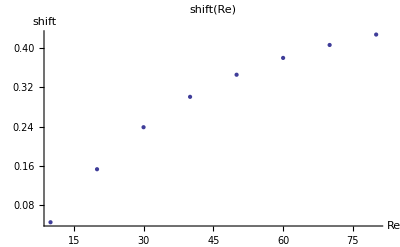
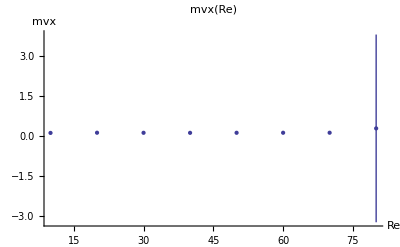
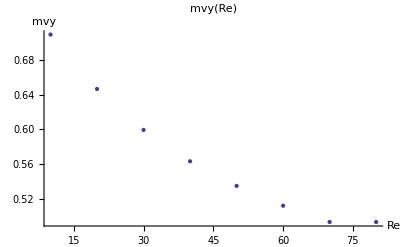
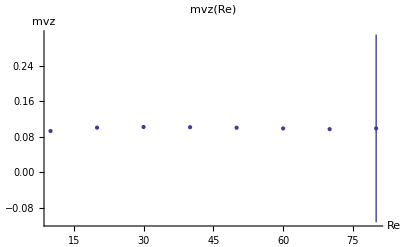
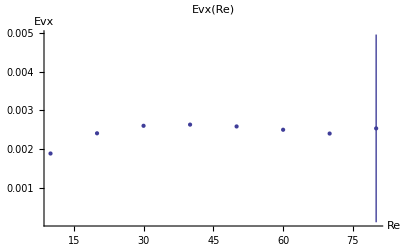
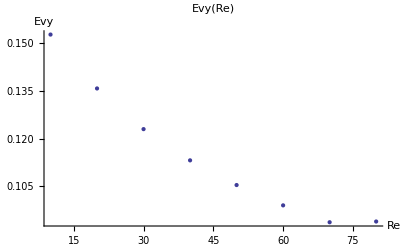
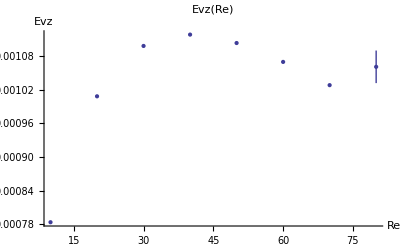
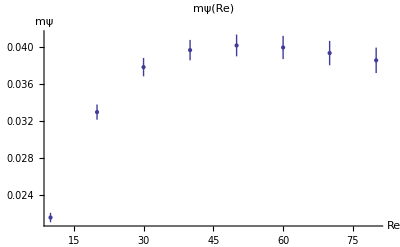

```mathematica
ShowDependance["Re",allfuncs,{"F(r)"->"1"}]
```

All data matches (True):

All such parameters={10,20,30,40,50,60,70,80,90,100,110,128,256}

{Re,r/R,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Re→1,r/R→0.25,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=11

№2:{Re→150,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№3:{Re→100,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№4:{Re→90,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№5:{Re→80,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№6:{Re→10,r/R→0.05,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№7:{Re→70,r/R→0.1,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№8:{Re→70,r/R→0,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№9:{Re→40,r/R→0.2,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№10:{Re→40,r/R→0.1,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

So constant parameters are:

{Re→1,r/R→0.25,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

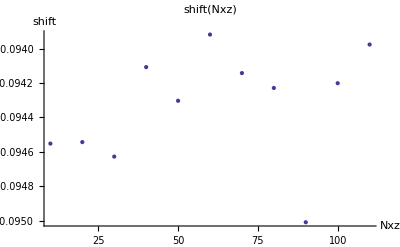
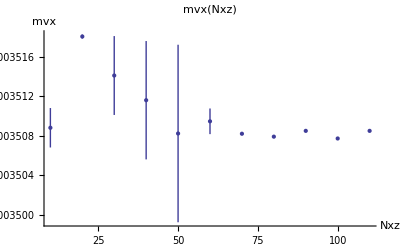
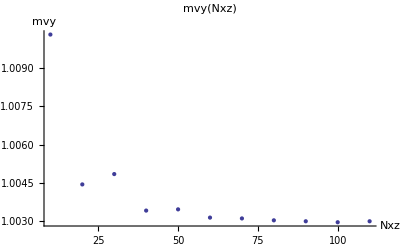
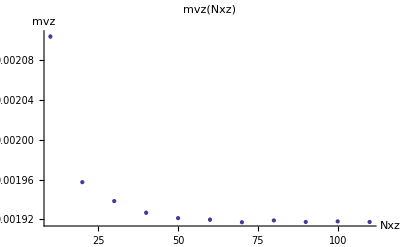
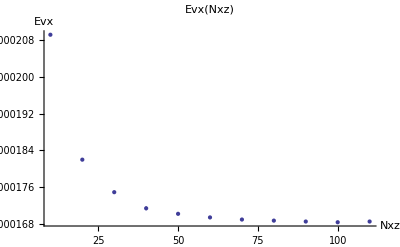
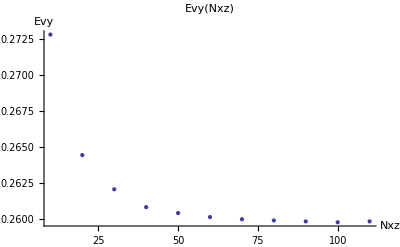
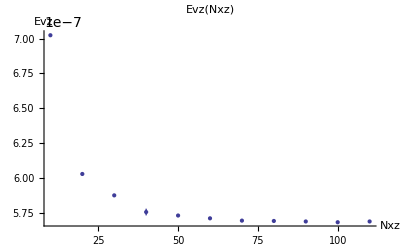
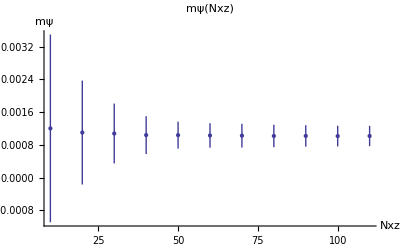

```mathematica
ShowDependance["Nxz",allfuncs]
```

```mathematica
pts//TableForm
```

```mathematica
Export[ToString[Unique[]]<>".eps",#]&/@{}
```

{$17.eps,$18.eps,$19.eps,$20.eps,$21.eps,$22.eps,$23.eps,$24.eps}

### Отдельное рисование

```mathematica
numfunc=4;
```

```mathematica
list=(Transpose[{First/@pts,{#⟦1⟧,#⟦2⟧}&/@(#[[numfunc]]&/@pts)}];
Transpose[{(1/First[#])^-1&/@pts,First[#]&/@(#[[numfunc]]&/@pts)}])
```

```mathematica
ListPlot[Drop[list,2],PlotRange->All,PlotLabel->Last[Last[(#1⟦numfunc⟧&)/@pts]],PlotStyle->PointSize[0.03]]
```

```mathematica
Transpose[pts[[All,2;;-2]]]
```

```mathematica
With[{param="lfi"},ListPlot[Transpose[{First/@pts,First/@#}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")"]&/@Transpose[pts[[All,2;;-2]]]
]
```

```mathematica
Transpose[{First/@pts,First/@pts[[All,8]]}]
```

{{0.01,3.66375},{0.1,0.00100646},{1.,0.00100646},{2 π,0.00100646}}

```mathematica
ListPlot[Rest@Transpose[{First/@pts,First/@pts[[All,8]]}]]
```

```mathematica
ListPlot[(First/@pts[[All,5]])]
```

```mathematica
With[{param="Re"},ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All]&/@Transpose[pts[[All,2;;-2]]]
]
```

```mathematica
Fit[Drop[list,2],{1,x},x]
```

0.990812+2.49089 x

```mathematica
PrintRange[GetFields[#,{"Re","shift"}]&/@$res]
```